## Using Genetic Algorithms to Find Equilibrium Bidding Strategies for Insurance Auctions

A common value auction is an auction in which the cost or value of the good or service being sold is the same for every bidder. A common value procurement auction is one where sellers compete to sell something that would cost any of them the same to provide. For example, suppose a company solicits bids from several insurance companies to sell it a commercial insurance policy. This is a procurement auction, and if the losses and other expenses incurred under the policy are only affected by the client, not by the insurer, then it is a common value procurement auction. In fact, most insurance sales can be described like this.

Many large insurance sales work like a simple sealed bid common value auction: The potential client provides a standard submission, including details of their exposure to risk and historical losses, to several insurers. Each insurer separately commissions one of their underwriters to review the submission. The underwriter reviews the submission in the context of their own unique experience in the insurance industry and distills his opinion down to an estimate of the total costs that will be incurred if her insurer writes a policy covering the client. This opinion is a private “signal” for the insurer. The insurer takes this signal and decides how much premium to ask for, in the form of an insurance quote given back to the client.

In practice the client, or an insurance broker acting on their behalf, may share information from these quotes with the other insurers, in hopes of getting a better deal. For now, though, let’s consider what should happen if the client simply picks whichever insurer gave the lowest quote, and buys a policy from them. The key details we need, to do this, are the number of insurers, and probability distributions of the signals and of the cost of providing coverage.

One case that is particularly well-studied is where the signals are uniformly distributed on the same interval and the expected total cost of providing coverage is equal to the average of the signals. See, for example,  Justin Smith: "Insurance Ratemaking and Auction Theory", Variance 17 (2), 2024. This case has a unique and easily found Nash equilibrium in which the bidders use bidding strategies that are linear in the value of the signal they receive.

But it’s quite unrealistic to assume that signals are uniformly distributed. In most practical applications it’s more reasonable to assume a unimodal distribution with relatively thin tails. It’s not immediately obvious what precise form of distribution is most appropriate, however, and for most such distributions the analytic forms of Nash equilibrium strategies are not easy to find, if they exist at all. It seems much more practical, then, to use numerical methods to find Nash equilibrium bidding strategies, and in particular to find a numerical approach that can be used efficiently with a wide variety of distributional assumptions. In this short notebook I’ll explore one such approach, with uses an artificial genetic algorithm (for a general introduction to genetic algorithms, see Melanie Mitchell: "An Introduction to Genetic Algorithms", MIT Press, 1996). I’ll represent common value first price sealed bid procurement auctions with two bidders, including bidding functions, signal distributions, etc., and use artificial genetic algorithms to find optimal bidding functions numerically.

### Symmetric Signal Distributions

With symmetric signal distributions and each signal having a similar effect on value, we can reasonably assume a symmetric equilibrium, so we only need to find a bidding function for one bidder. This example assumes the signals are given by a binormal copula over two censored normal distributions on the unit interval.

```mathematica
sDist=NormalDistribution[0.5,0.3];
sigDist=CensoredDistribution[{{0,1},{0,1}},
CopulaDistribution[{"Binormal",0.9},{
sDist,sDist}]];
```

The following graph shows the CDF of one of the signal distributions.

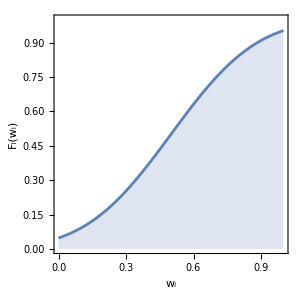

```mathematica
Plot[CDF[sDist,x],{x,0,1},AspectRatio->1,PlotRange->{{0,1},{0,1}},ImageSize->300,Frame->True,Filling->Axis,FrameLabel->{"w_i","F_i(w_i)"},LabelStyle->Directive[Darker[Gray],Small]]
```

The next graph plots a sample of signal pairs from the joint distribution. Note the densest clustering in the middle of the domain, with less dense tails where both signals are either low or high.

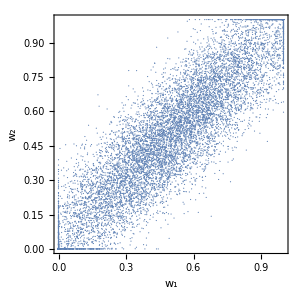

```mathematica
ListPlot[RandomVariate[sigDist,10000],AspectRatio->1,PlotRange->{{0,1},{0,1}},Frame->True,ImageSize->300,FrameLabel->{"w_1","w_2"},LabelStyle->Directive[Darker[Gray],Small]]
```

Next, specify that the actual cost of providing coverage is a weighted average of the two signals. We’re assuming each signal has a similar effect, so the weight on each is equal.

```mathematica
cost[signals_,k1_:0.5]:=k1 signals[[1]]+(1-k1)signals[[2]]
```

Now specify a very general form for the bid function. This uses a piecewise linear function, which (with enough pieces) should be sufficiently flexible.

```mathematica
bidFn[list_]:=ListInterpolation[list,{{0,1}},InterpolationOrder->1]
```

The next function operates on a specific pair of bid functions and specific signals for each bidder, and tells us the expected profit for each bidder. Since the loser gets zero, it also tells us who won the auction.

```mathematica
auction[bidf_,sig_,k1_:0.5]:=Module[{bids,c,winner,outcome},
bids=#[[1]][#[[2]]]&/@Transpose[{bidf,sig}];
winner=Position[bids,Min[bids]][[1,1]];
c=cost[sig,k1];
outcome=ReplacePart[{0,0},winner->bids[[winner]]-c]]
```

The next function is used to create a random bid function. We can easily show that the bid function must be higher than the signal value, non-decreasing, and pass through [1,1]. Every generated function will obey these basic rules. The random bid functions are the starting points for the evolutionary process. It may be possible to refine the specification here to make the overall algorithm more efficient, by providing “better” starting points.

```mathematica
rndBF[n_]:=Module[{v,w=0,x},
Append[
Table[
x=Max[i,w];
v=RandomVariate[TriangularDistribution[{x,1},x]];
w=v;
w
,{i,0,1-1/n,1/n}]
,1]]
```

Next generate a “population” of random bid functions. The number of pieces in a bid function and the number of functions are hyperparameters. The following graph plots the functions.

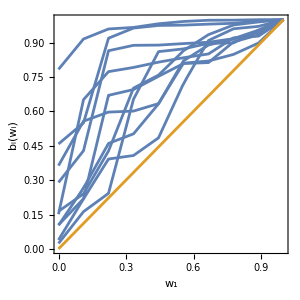

```mathematica
bt=Table[rndBF[9],10];
bf=bidFn[#]&/@bt;
Plot[Flatten[{#[x]&/@bf,{x}},1]//Evaluate,{x,0,1},PlotRange->{{0,1},{0,1}},Frame->True,AspectRatio->1,ImageSize->300,PlotStyle->Append[Table[RGBColor[0.368417, 0.506779, 0.709798],10],RGBColor[0.880722, 0.611041, 0.142051]],FrameLabel->{"w_1","b_i(w_i)"},LabelStyle->Directive[Darker[Gray],Small]]
```

The specification of each bid function is like its genetic code.  The following code runs a simple process of “evolution” for the population of bid functions. To determine their “fitness”, the functions are set against each other in a round robin tournament at the beginning of each evolutionary step. The very most most successful bid functions in each tournament survive to the next step, and the next most successful are combined by averaging in a series of combinations to produce the bulk of a population for the next step. Some new random bid functions are also added at each step (think of them as immigrants) to slow the process of evolution and reduce the chance of converging on a local optimum. This is a simplified version of a genetic algorithm, which I think works quite well.

```mathematica
Quiet[CloseKernels[]];
Quiet[LaunchKernels[]];
```

```mathematica
roundRobin[sn_,bt_,bf_,n_,rounds_,sigDist_]:=Module[{s,rrs,res},
s=RandomVariate[sigDist,sn];rrs=ParallelMap[With[{round=#},Plus@@#&/@Transpose[auction[bf[[round]],#]&/@s]]&,rounds];res=ParallelTable[{i,Plus@@Select[Transpose[{Flatten[rounds],Flatten[rrs]}],#[[1]]==i&][[All,2]]},{i,1,n}];rss=SortBy[res,Last]
]
```

```mathematica
mix[bt_]:=Module[{rp,w,mut=4},
rp=Partition[RandomSample[bt],2];
Mean[WeightedData[#,{w=RandomVariate[BetaDistribution[mut,mut]],1-w}]]&/@rp
]
```

```mathematica
nextGen[rss_,pt_,n_,topFew_,mixTop_,mixToT_]:=Module[{bt,bf},
bt=Flatten[{nt[[rss[[-topFew;;]]]],
mix[nt[[rss[[-topFew-mixTop;;-topFew-1]]]]],
mix[nt[[rss[[-mixToT;;]]]]],
Table[rndBF[pt],n-topFew-mixTop/2-mixToT/2]
},1];
nf=bidFn[#]&/@bt;
nt=bt;
]
```

```mathematica
genA[sigDist_,t_:5,n_:20,pt_:2,sn_:1000]:=Module[{rounds,bt,bf,topFew=2,mixTop=10,mixToT=6},
(* specify pairings for a round robin of bid functions indexed from 1 to n: *)
rounds=Flatten[Table[{i,j},{i,1,n},{j,1,i}],1];
(* create a seed set of bid functions: *)
bt=Table[rndBF[pt],n];
bf=bidFn[#]&/@bt;
(* round robin on the seed set: *)
rss=roundRobin[sn,bt,bf,n,rounds,sigDist];
(* now run the genetic algorithm through the generations: *)
nt=bt;
nf=bf;
Monitor[Do[
nextGen[rss[[All,1]],pt,n,topFew,mixTop,mixToT];
rss=roundRobin[sn,nt,nf,n,rounds];
,{i,t}],i];
]
```

```mathematica
Timing[genA[sigDist,100,20,9,10000]]
```

{1396.09,Null}

The following graph shows part of the evolved population of bid functions. If we have simulated enough evolution then they should look fairly similar.

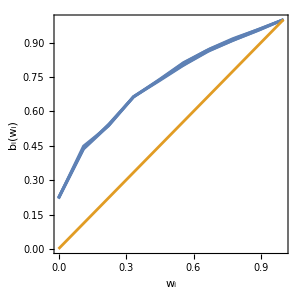

```mathematica
m=4;
Plot[Flatten[{nf[[#]][x]&/@rss[[-m;;,1]],{x}},1]//Evaluate,{x,0,1},PlotRange->{{0,1},{0,1}},Frame->True,AspectRatio->1,ImageSize->300,FrameLabel->{"w_i","b_i(w_i)"},LabelStyle->Directive[Darker[Gray],Small],PlotStyle->Append[Table[RGBColor[0.368417, 0.506779, 0.709798],m],RGBColor[0.880722, 0.611041, 0.142051]]]
```

Finally, derive a single bid function by averaging together the final population. Under the assumption of symmetry, this should be a Nash equilibrium bid function for both bidders.

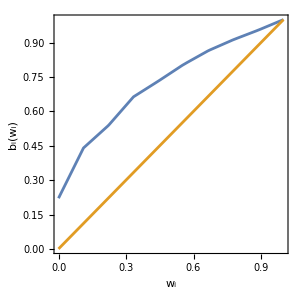

```mathematica
mean=Mean[WeightedData[#,{0.2,0.3,0.5}]]&/@Transpose[nt[[rss[[-3;;,1]]]]];
Plot[{bidFn[mean][x],x},{x,0,1},PlotRange->{{0,1},{0,1}},Frame->True,AspectRatio->1,ImageSize->300,FrameLabel->{"w_i","b_i(w_i)"},LabelStyle->Directive[Darker[Gray],Small]]
```